# Modne besede – najbolj priljubljene besede s področja tehnologije in računalništva skozi leta

## Podatki

```mathematica
modnBes= {"Computer", "Software", "Algorithm", "Data", "Internet", "Website", "Browser","Bitcoin", "Blockchain", "Cryptocurrency"};
```

To so besede, ki sem jih izbral za analizo s pomočjo orodja "WordFrequencyData" . Izogibal sem se besedam, kot je cloud, ali kratkim okrajšavam (kot sta LLM ali AI), saj bi bile preveč splošne in podatki ne bi bili dovolj natančni .

## Splošni izrazi

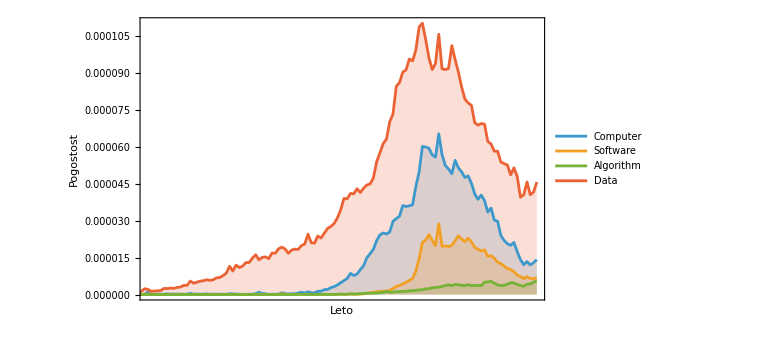

```mathematica
computer = WordFrequencyData["Computer", "TimeSeries"];
software= WordFrequencyData["Software", "TimeSeries"];
algorithm = WordFrequencyData["Algorithm", "TimeSeries"];
data = WordFrequencyData["Data", "TimeSeries"];

DateListPlot[{computer, software, algorithm, data}, PlotLegends->{"Computer", "Software", "Algorithm", "Data"}, ImageSize->Large,FrameLabel->{"Leto", "Pogostost"}, Filling->Axis, PlotTheme->"Detailed", PlotRange->{{1900, Full}, Full}]
```

Zdi se, da so vse te besede dosegle vrhunec okoli leta 1990 (z izjemo besede algoritem), medtem ko sem pričakoval, da bodo te besede dosegle vrhunec okoli leta 2000.

## Besede, povezane z internetom

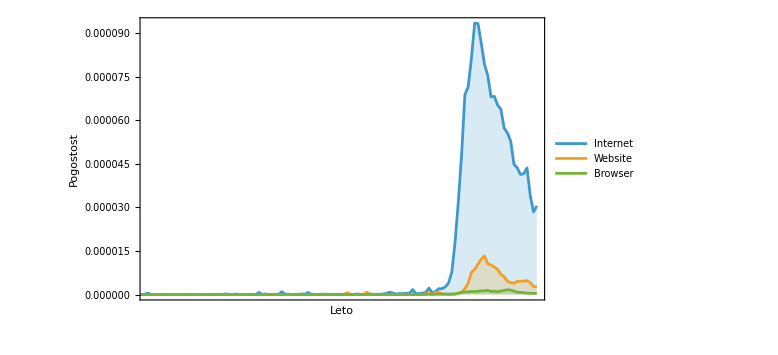

```mathematica
internet = WordFrequencyData["Internet", "TimeSeries"];
website = WordFrequencyData["Website", "TimeSeries"];
browser = WordFrequencyData["Browser", "TimeSeries"];

DateListPlot[{internet, website, browser}, PlotLegends->{"Internet", "Website", "Browser"}, ImageSize->Large,FrameLabel->{"Leto", "Pogostost"}, Filling->Axis, PlotTheme->"Detailed", PlotRange->{{1900, Full}, Full}]
```

Te besede so dosegle vrhunec okoli leta 2000, pri čemer je tokratna izjema beseda browser, ki se v primerjavi z drugimi besedami ne zdi, da bi bila pogosto omenjena.

## Besede, povezane s kriptovalutami

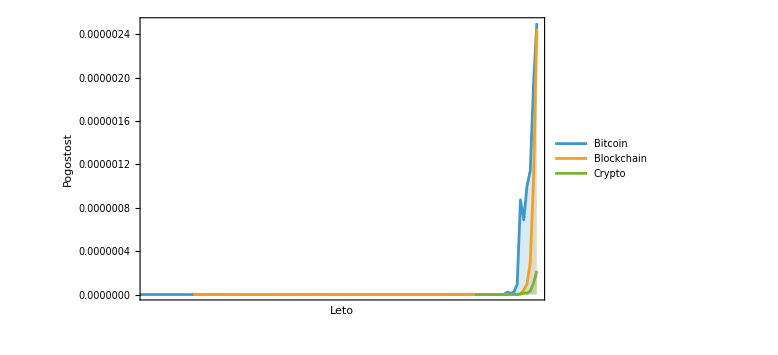

```mathematica
bitcoin = WordFrequencyData["Bitcoin", "TimeSeries"];
blockchain = WordFrequencyData["Blockchain", "TimeSeries"];
crypto = WordFrequencyData["Cryptocurrency", "TimeSeries"];

DateListPlot[{bitcoin, blockchain, crypto}, PlotLegends->{"Bitcoin", "Blockchain", "Crypto"}, ImageSize->Large,FrameLabel->{"Leto", "Pogostost"}, Filling->Axis, PlotTheme->"Detailed", PlotRange->{{1900, Full}, Full}]
```

Tokrat vse besede (kot je bilo pričakovati) sledijo istemu trendu, a je vseeno malo nenavadno, da se o njih prej sploh ni govorilo, nato pa so v zadnjih 10 letih tako strmo poskočile.

## Spletna aplikacija

```mathematica
cloudModnBes = CloudDeploy[Manipulate[DateListPlot[WordFrequencyData[Beseda, "TimeSeries"],PlotTheme->"Detailed",ImageSize -> Large, FrameLabel->{"Leto", "Pogostost"}, Filling->Axis, PlotRange->{{1900, Full}, Full}], {{Beseda, First[modnBes], "Modna Beseda"}, modnBes}], Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/c8159850-79d7-4c77-a05b-3c37792451e6]

## Videoposnetek

https://youtu.be/hbhArvdqA5k?si=TqjbpkM7Q9J2Dujt